```mathematica
MyEll[center_,covMat_,f_]:=RegionPlot3D[Dot[{x-center⟦1⟧,y-center⟦2⟧,z-center⟦3⟧},Inverse[covMat].{x-center⟦1⟧,y-center⟦2⟧,z-center⟦3⟧}]<f,
{x,center⟦1⟧-Sqrt[f]*Sqrt[Max[Eigenvalues[covMat]]],center⟦1⟧+Sqrt[f]*Sqrt[Max[Eigenvalues[covMat]]]},
{y,center⟦2⟧-Sqrt[f]*Sqrt[Max[Eigenvalues[covMat]]],center⟦2⟧+Sqrt[f]*Sqrt[Max[Eigenvalues[covMat]]]},
{z,center⟦3⟧-Sqrt[f]*Sqrt[Max[Eigenvalues[covMat]]],center⟦3⟧+Sqrt[f]*Sqrt[Max[Eigenvalues[covMat]]]},
PlotStyle->Directive[Yellow,Opacity[0.2]],Mesh->None]
```

-Graphics3D-

```mathematica
f=ToExpression[data⟦1⟧];
center = ToExpression[StringSplit[data⟦2⟧," "]];
covMat = ToExpression[{StringSplit[data⟦3⟧," "],StringSplit[data⟦4⟧," "],StringSplit[data⟦5⟧," "]}];
points=Table[ ToExpression[StringSplit[data⟦i⟧," "]],{i,6,Dimensions[data]⟦1⟧}];
rainbow = Table[Select[points,i/2<#⟦4⟧&&#⟦4⟧<(i+1)/2&],{i,0,6}];
Show[
ListPointPlot3D[rainbow⟦All,All,1;;3⟧],
MyEll[center,covMat,f]
]
```

-Graphics3D-

```mathematica
Manipulate[ListPointPlot3D[rainbow⟦i,All,1;;3⟧],{i,1,Dimensions[rainbow]⟦1⟧,1}]
```

```mathematica
ListPointPlot3D[Table[Select[points,i<#⟦4⟧&&#⟦4⟧<i+1&],{i,0,11}]⟦All,All,1;;3⟧]
```

-Graphics3D-

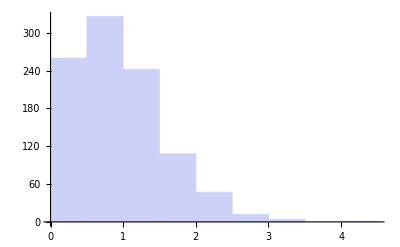

```mathematica
Histogram[points[[All,4]],10]
```